```mathematica
ClearAll["Global`*"]
```

```mathematica
K[n_,k_] := K[n,k]=Sum[ FullSimplify[MangoldtLambda[j]/Log[j]] K[Floor[n/j],k-1],{j,2,n}];K[n_,0]:=1

E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1

EM2[n_,a_,b_] := EM2[n,a,b]=Sum[(-1)^k Binomial[k-1,k-a]E2a[n,k,b],{k,1,Log[If[b<2,b,2],n]}];EM2[n_,0,b_]:=1
E2d[n_,a_,b_] := E2d[n,a,b]=Sum[(-1)^s Binomial[s-1,s-a]EM2[n,s,b],{s,1,Log[If[b<2,b,2],n]}];E2d[n_,0,b_]:=1
E1e[n_,k_,b_]:=Sum[FactorialPower[k,a]/a! E2d[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
D1g[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j E1e[n/b^j,k,b],{j,0,Log[b,n]}]
D1h[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j (Sum[FactorialPower[k,a]/a! E2d[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n]}]),{j,0,Log[b,n]}]

D1i[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j (1+Sum[FactorialPower[k,a]/a! (Sum[(-1)^s Binomial[s-1,s-a]EM2[n/b^j,s,b],{s,1,Log[If[b<2,b,2],n/b^j]}]),{a,1,Log[If[b>2,2,b],n]}]),{j,0,Log[b,n]}]
D1j[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j (1+Sum[FactorialPower[k,a]/a! (Sum[(-1)^s Binomial[s-1,s-a]EM2[n/b^j,s,b],{s,1,Log[If[b<2,b,2],n/b^j]}]),{a,1,Log[If[b>2,2,b],n]}]),{j,0,Log[b,n]}]

EP2[n_,a_,b_] := EP2[n,a,b]=Sum[SeriesCoefficient[Series[(Log[x+1])^a,{x,0,230}],k]E2a[n,k,b],{k,1,Log[If[b>2,2,b],n]}];EP2[n_,0,b_]:=1
E1p[n_,a_,b_] := E1p[n,a,b]=1+Sum[a^k/k! EP2[n,k,b],{k,1,Log[If[b>2,2,b],n]}]
D1f[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j E1p[n/b^j,k,b],{j,0,Log[b,n]}]


D1f2[n_, a_, b_] := Sum[ Binomial[a+j-1,a-1] b^j (1+Sum[a^k/k! EP2[n/b^j,k,b],{k,1,Log[If[b>2,2,b],n/b^j]}]),{j,0,Log[b,n]}]
D1f3[n_, a_, b_] := Sum[ Binomial[a+j-1,a-1] b^j a^k/k! EP2[n/b^j,k,b],{j,0,Log[b,n]},{k,0,Log[If[b>2,2,b],n/b^j]}]
D1f3a[n_, a_, b_] := Grid[Table[ Binomial[a+j-1,a-1] b^j a^k/k! EP[n/b^j,k,b],{j,0,Log[b,n]},{k,0,Log[If[b>2,2,b],n/b^j]}]]
D1f3a2[n_, a_, b_] := Grid[Table[ Binomial[a+j-1,a-1] b^j a^k/k! EP[n/b^j,k,b]/a,{j,0,Log[b,n]},{k,0,Log[If[b>2,2,b],n/b^j]}]]
D1f3b[n_, a_, b_] := Grid[Table[ Binomial[a+j-1,a-1] b^j a^k/k! EP2[n/b^j,k,b],{j,0,Log[b,n]},{k,0,Log[If[b>2,2,b],n/b^j]}]]
```

```mathematica
D1j[100,2,2]
```

482

```mathematica
D1f3[100,-1,1.2]
```

1.

```mathematica
D1f3a[100,-1,2]
```

EP[100,0,2] | -EP[100,1,2] | 1/2 EP[100,2,2] | -1/6 EP[100,3,2] | 1/24 EP[100,4,2] | -1/120 EP[100,5,2] | 1/720 EP[100,6,2]
-2 EP[50,0,2] | 2 EP[50,1,2] | -EP[50,2,2] | 1/3 EP[50,3,2] | -1/12 EP[50,4,2] | 1/60 EP[50,5,2] | 
0 | 0 | 0 | 0 | 0 |  | 
0 | 0 | 0 | 0 |  |  | 
0 | 0 | 0 |  |  |  | 
0 | 0 |  |  |  |  | 
0 |  |  |  |  |  |

```mathematica
D1f3b[100,-1,1.2]
```

1. | 4.1506 | 6.08731 | 5.07149 | 2.85546 | 0.411142 | 0.219317 | 0.161956 | 0.037866 | 0.00671787 | 0.00252624 | 0.000656331 | 0.000105289 | 0.0000119036 | 1.24035×10^-6 | 1.3385×10^-7 | 1.28887×10^-8 | 9.80752×10^-10 | 5.65068×10^-11 | 2.41942×10^-12 | 7.60268×10^-14 | 1.72903×10^-15 | 2.77399×10^-17 | 2.99615×10^-19 | 1.97317×10^-21 | 6.15015×10^-24
-1.2 | -2.8017 | -5.7052 | -5.80447 | -2.27484 | -0.608456 | -0.414726 | -0.158911 | -0.0247354 | -0.00839147 | -0.00298941 | -0.000643128 | -0.0000879832 | -0.0000100652 | -1.182×10^-6 | -1.2773×10^-7 | -1.10288×10^-8 | -7.19869×10^-10 | -3.46811×10^-11 | -1.21576×10^-12 | -3.05977×10^-14 | -5.39292×10^-16 | -6.36069×10^-18 | -4.55111×10^-20 | -1.53754×10^-22 | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

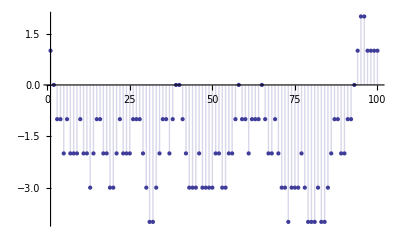

```mathematica
DiscretePlot[ D1f3[ n,-1,2], {n,1,100}]
```

```mathematica
D1i[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j (1+Sum[FactorialPower[k,a]/a! (Sum[(-1)^s Binomial[s-1,s-a]EM2[n/b^j,s,b],{s,1,Log[If[b<2,b,2],n/b^j]}]),{a,1,Log[If[b>2,2,b],n]}]),{j,0,Log[b,n]}]

D1j[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j (1+Sum[Sum[FactorialPower[k,a]/a! (-1)^s Binomial[s-1,s-a]EM2[n/b^j,s,b],{s,1,Log[If[b<2,b,2],n/b^j]}],{a,1,Log[If[b>2,2,b],n]}]),{j,0,Log[b,n]}]

D1k[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j (1+Sum[
FactorialPower[k,a]/a! (-1)^s Binomial[s-1,s-a]EM2[n/b^j,s,b],{a,1,Log[If[b>2,2,b],n]},{s,1,Log[If[b<2,b,2],n/b^j]}
]),{j,0,Log[b,n]}]
```

```mathematica
D1m[n_, k_, b_] := Sum[  (Binomial[k+j-1,k-1] b^j+Sum[
Binomial[k+j-1,k-1] b^j FactorialPower[k,a]/a! (-1)^s Binomial[s-1,s-a]EM2[n/b^j,s,b],{a,1,Log[If[b>2,2,b],n]},{s,1,Log[If[b<2,b,2],n/b^j]}
]),{j,0,Log[b,n]}]

D1n[n_, k_, b_] := Sum[Binomial[k+j-1,k-1] b^j,{j,0,Log[b,n]}]+ Sum[  (Sum[
Binomial[k+j-1,k-1] b^j FactorialPower[k,a]/a! (-1)^s Binomial[s-1,s-a]EM2[n/b^j,s,b],{a,1,Log[If[b>2,2,b],n]},{s,1,Log[If[b<2,b,2],n/b^j]}
]),{j,0,Log[b,n]}]

D1o[n_, k_, b_] := Sum[Binomial[k+j-1,k-1] b^j,{j,0,Log[b,n]}]+ Sum[  Binomial[k+j-1,k-1] b^j FactorialPower[k,a]/a! (-1)^s Binomial[s-1,s-a]EM2[n/b^j,s,b],{j,0,Log[b,n]},{a,1,Log[If[b>2,2,b],n]},{s,1,Log[If[b<2,b,2],n/b^j]}]
```

```mathematica
D1o[100,2,2]
```

482

```mathematica
D1p[n_, k_, b_] := Sum[Binomial[k+j-1,k-1] b^j,{j,0,Log[b,n]}]+ Sum[  Binomial[k+j-1,k-1] b^j FactorialPower[k,a]/a! (-1)^s Binomial[s-1,s-a]em2[n/b^j,s,b],{a,1,Log[If[b>2,2,b],n]},{j,0,Log[b,n]},{s,1,Log[If[b<2,b,2],n/b^j]}]

D1p[100,1,7]
```

57-49 em2[100/49,1,7]-7 em2[100/7,1,7]+7 em2[100/7,2,7]-7 em2[100/7,3,7]-em2[100,1,7]+em2[100,2,7]-em2[100,3,7]+em2[100,4,7]-em2[100,5,7]+em2[100,6,7]

```mathematica
ff[n_, b_, k_] :=Sum[ FactorialPower[k,a]/a!,{a,0,Floor[Log[If[b<2,b,2],n]]}]
```

```mathematica
ff[100,1.1,-3]
```

625

```mathematica
(2^2)-1
```

3

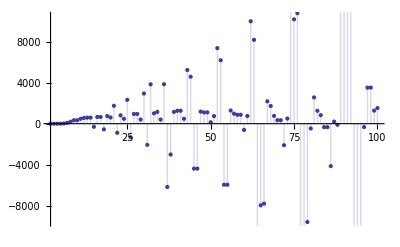

```mathematica
DiscretePlot[EP2[n,8,1.2],{n,2,100}]
```

```mathematica
D1f3a[100,1,2]
```

EP[100,0,2] | EP[100,1,2] | 1/2 EP[100,2,2] | 1/6 EP[100,3,2] | 1/24 EP[100,4,2] | 1/120 EP[100,5,2] | 1/720 EP[100,6,2]
2 EP[50,0,2] | 2 EP[50,1,2] | EP[50,2,2] | 1/3 EP[50,3,2] | 1/12 EP[50,4,2] | 1/60 EP[50,5,2] | 
4 EP[25,0,2] | 4 EP[25,1,2] | 2 EP[25,2,2] | 2/3 EP[25,3,2] | 1/6 EP[25,4,2] |  | 
8 EP[25/2,0,2] | 8 EP[25/2,1,2] | 4 EP[25/2,2,2] | 4/3 EP[25/2,3,2] |  |  | 
16 EP[25/4,0,2] | 16 EP[25/4,1,2] | 8 EP[25/4,2,2] |  |  |  | 
32 EP[25/8,0,2] | 32 EP[25/8,1,2] |  |  |  |  | 
64 EP[25/16,0,2] |  |  |  |  |  |

```mathematica
D1f3a[100,-1,2]
```

EP[100,0,2] | -EP[100,1,2] | 1/2 EP[100,2,2] | -1/6 EP[100,3,2] | 1/24 EP[100,4,2] | -1/120 EP[100,5,2] | 1/720 EP[100,6,2]
-2 EP[50,0,2] | 2 EP[50,1,2] | -EP[50,2,2] | 1/3 EP[50,3,2] | -1/12 EP[50,4,2] | 1/60 EP[50,5,2] | 
0 | 0 | 0 | 0 | 0 |  | 
0 | 0 | 0 | 0 |  |  | 
0 | 0 | 0 |  |  |  | 
0 | 0 |  |  |  |  | 
0 |  |  |  |  |  |

```mathematica
D1f3a2[100,.0000001,2]
```

1.×10^7 EP[100,0,2] | 1. EP[100,1,2] | 5.×10^-8 EP[100,2,2] | 1.66667×10^-15 EP[100,3,2] | 4.16667×10^-23 EP[100,4,2] | 8.33333×10^-31 EP[100,5,2] | 1.38889×10^-38 EP[100,6,2]
2. EP[50,0,2] | 2.×10^-7 EP[50,1,2] | 1.×10^-14 EP[50,2,2] | 3.33333×10^-22 EP[50,3,2] | 8.33333×10^-30 EP[50,4,2] | 1.66667×10^-37 EP[50,5,2] | 
2. EP[25,0,2] | 2.×10^-7 EP[25,1,2] | 1.×10^-14 EP[25,2,2] | 3.33333×10^-22 EP[25,3,2] | 8.33333×10^-30 EP[25,4,2] |  | 
2.66667 EP[25/2,0,2] | 2.66667×10^-7 EP[25/2,1,2] | 1.33333×10^-14 EP[25/2,2,2] | 4.44445×10^-22 EP[25/2,3,2] |  |  | 
4. EP[25/4,0,2] | 4.×10^-7 EP[25/4,1,2] | 2.×10^-14 EP[25/4,2,2] |  |  |  | 
6.4 EP[25/8,0,2] | 6.4×10^-7 EP[25/8,1,2] |  |  |  |  | 
10.6667 EP[25/16,0,2] |  |  |  |  |  |

```mathematica
(D1f3[100,aa=.00001,2]-1)/aa
```

28.5338

```mathematica
EP2[100,1,1.02]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$Aborted

```mathematica
D1ha[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j (Sum[FactorialPower[k,a]/a! E2d[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n]}]),{j,0,Log[b,n]}]
```

```mathematica
D1ha[100,1,2]
```

100

```mathematica
D1hb[n_, k_, b_] := Sum[ (Sum[Binomial[k+j-1,k-1] b^j FactorialPower[k,a]/a! E2[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n]}]),{j,0,Log[b,n]}]
```

```mathematica
D1hb[100,1,2]
```

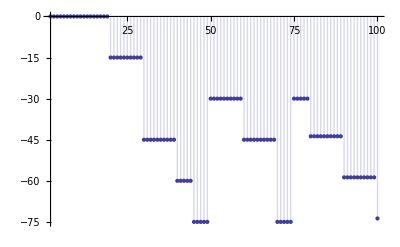

```mathematica
DiscretePlot[EP2[n,3,5]-K[n,3],{n,2,100}]
```

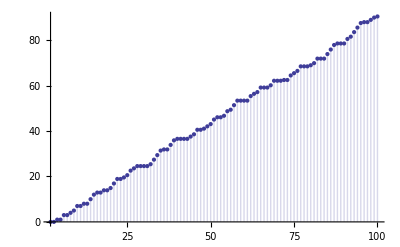

```mathematica
DiscretePlot[K[n,2],{n,2,100}]
```